```mathematica
(*<<DiscreteMath`ComputationalGeometry`*)
(*Needs["Splines`"]*)
<<ComputationalGeometry`

Off[General::spell1]
Inp=OpenRead["C://Users//nikos//Documents//My Work//raw//x-ray_1.txt"];
points=ReadList[Inp,{Number,Number}];
Xlist=Transpose[points][[1]];
Ylist=Transpose[points][[2]];
Dtor=N[Pi/180];
Theta=90;
f[x_]=0 ⅇ^(-50( x*Dtor-(2*(Theta-8)*Dtor))^2)+0 ⅇ^(-30( x*Dtor-(2*(Theta+11)*Dtor))^2);
Mixed=Table[{Xlist[[i]],Ylist[[i]]+f[Xlist[[i]]]+ 0Random[]},{i,1,Length[Ylist]}];
Export["C://Users//nikos//Documents//My Work//raw//x-ray_1.xy",Mixed,"CSV"];
Ylist=Transpose[Mixed][[2]];
mx=Max[Ylist]
P0=ListPlot[Mixed,Joined->True,PlotStyle->{RGBColor[0,0,0]},PlotRange->{Automatic,{-10,mx}}];
```

2002.

```mathematica
The Signal is assumed as a composition of a low Frequency component (background) and the true informational signal.
By low filtering (controlled by a variable called j )we extract from the composite signal a part which is similar in the true background component. 
This low frequency signal is quite similar to the true background but not exact.
```

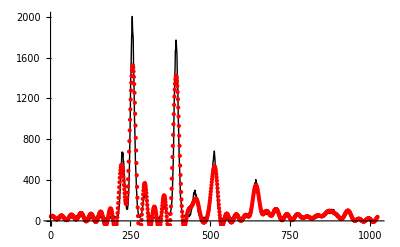

```mathematica
Fr=Fourier[Ylist];(*simple windowing by appeding nulls at ends*)
tbl={};
j=34;(*low filter components this is variable 1*)
Table[If[i<j||i>Length[Fr]-j,Fr[[i]],0],{i,1,Length[Fr]}];

InverseFourier[%];
Res=Re[Partition[Flatten[Table[{Mixed[[i]][[1]],%[[i]]},{i,1,Length[%]}]],2]];
P2=ListPlot[Re[Res],PlotStyle->{RGBColor[1,0,0]},PlotRange->{Automatic,{-10,mx}}];
Show[P0,P2]
Bins=Table[If[Res[[i+1]][[2]]>Res[[i]][[2]],1,0],{i,1,Length[Res]-1}];
S="";
For[i=1,i<Length[Res],i++,If[Res[[i+1]][[2]]>Res[[i]][[2]],S=S<>"1",S=S<>"0"]];
tr=Append[Prepend[Transpose[StringPosition[S,{"01","10"}]][[1]],1],Length[Mixed]];(*Find peaks and valleys*)
```

CompiledFunction::cflist: Nontensor object generated; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction :: cflist will be suppressed during this calculation.

Total points reduced to: 223

Total points reduced to: 72

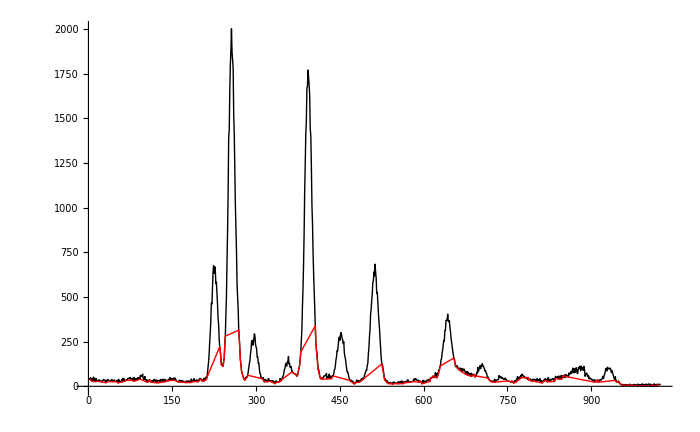

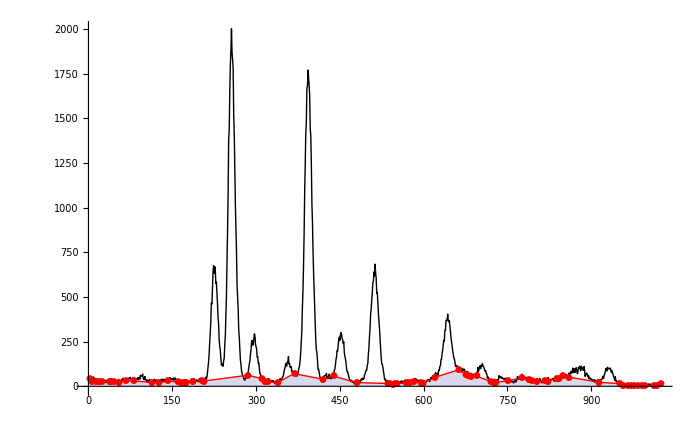

```mathematica
pts={};
joints=0.45;(* 1x mean derivative of all points*)
For[i=1,i<Length[tr],i++,lst=Table[{Mixed[[j]][[1]],Mixed[[j]][[2]]},{j,tr[[i]],tr[[i+1]]}];
Xtmp=Transpose[lst][[2]];
Md=Median[Xtmp];
cv=ConvexHull[lst];
For[k=1,k<=Length[cv],k++,
If[Xtmp[[cv[[k]]]]<Md,pts=Append[pts,cv[[k]]+tr[[i]]-1 ]]]; (*convex low*)
]
fpts=Sort[Flatten[pts]];
Print["Total points reduced to: ",Length[fpts]];
ConvexPts=Mixed[[fpts]];

(*YConvexlist=Transpose[ConvexPts][[2]];
FrConvex=Fourier[YConvexlist];
Print["Length of convex points:",Length[%]];
j=30;(*low filter components this is variable 1*)
Res1=Table[If[i<j||i>Length[FrConvex]-j,FrConvex[[i]],0],{i,1,Length[FrConvex]}];
InverseFourier[Res1];
ResConvex=Re[Partition[Flatten[Table[{ConvexPts[[i]][[1]],%[[i]]},{i,1,Length[%]}]],2]];
P5=ListPlot[Re[ResConvex],Joined->True,PlotStyle->{RGBColor[1,0,0]},PlotRange->{Automatic,{-10,mx}}];
Show[P0,P5]*)

bgrd=Mixed[[fpts]];
bgrd=DeleteCases[Table[If[bgrd[[i+1]][[1]]-bgrd[[i]][[1]]>=0.02,{bgrd[[i]][[1]],bgrd[[i]][[2]]}],{i,1,Length[bgrd]-1}],Null];
lambdas=Table[Abs[(bgrd[[i+1]][[2]]-bgrd[[i]][[2]])/(bgrd[[i+1]][[1]]-bgrd[[i]][[1]])],{i,1,Length[bgrd]-1}];
(*lambdas=Table[Abs[(bgrd[[i+1]][[1]]-bgrd[[i]][[1]])/(bgrd[[i+1]][[2]]-bgrd[[i]][[2]])],{i,1,Length[bgrd]-1}];*)
laavg=Median[lambdas]; (*median regression / overlap and add?*)
count=0;
For [i=1,i<Length[lambdas],i++,If[lambdas[[i]]> joints* laavg,count++]];
lapos=DeleteCases[Table[If[lambdas[[i]]> joints * laavg,i],{i,1,Length[lambdas]}],Null];
cntr=0;
For[i=1,i≤Length[lapos],i++,bgrd=Delete[bgrd,lapos[[i]]-cntr];cntr++]
Print["Total points reduced to: ",Length[bgrd]];
(*Append First and last point*)
bgrd=Prepend[bgrd,Mixed[[1]]];
bgrd=Append[bgrd,Mixed[[Length[Mixed]]]];
P3=ListPlot[bgrd,Joined->True,PlotStyle->{RGBColor[1,0,0]},Filling->Axis,PlotMarkers->Automatic, PlotRange->{Automatic,{0,mx}}];
P4=ListPlot[ConvexPts,Joined->True,PlotStyle->{RGBColor[1,0,0]},PlotRange->{Automatic,{-10,mx}}];
Show[P0,P4]
Show[P0,P3]
fnlst={};
(*Fig 1 Only Convex Selected by Median of related area
  Next Fig after replacing the edge points of the related area by *)
```

```mathematica
cv
```

{15,3,1,2,7,13,14}

```mathematica
lst
```

{{1010,6.},{1011,3.},{1012,14.},{1013,10.},{1014,11.},{1015,8.},{1016,4.},{1017,10.},{1018,12.},{1019,11.},{1020,9.},{1021,11.},{1022,9.},{1023,10.},{1024,14.}}

```mathematica
tr
```

{1,4,18,33,49,65,79,95,111,126,141,156,172,187,202,222,236,256,278,294,311,324,339,355,369,392,417,454,479,513,536,551,566,581,596,611,619,642,664,676,690,705,724,739,756,773,790,803,818,837,848,872,910,930,952,965,980,995,1010,1024}

```mathematica
{1,14,111,121,139,148,171,177,198,207,228,241,266,274,300,308,360,373,420,433,502,513,554,558,580,598,637,647,671,677,712,728,750,759,790,792,877,947,955,965,1065,1121,1129,1150,1165,1180,1192,1205,1218,1232,1249,1269,1303,1323,1331,1353,1390,1403,1423,1455,1476,1482,1494,1532,1553,1571,1580,1603,1624,1640,1660,1677,1693,1708,1720,1733,1749,1767,1785,1801,1809,1822,1873,1880,1882,1897,1913,1946,1947,2027,2044,2060,2074,2124,2131,2196,2210,2256,2268,2287,2297,2318,2325,2345,2356,2374,2377,2398,2411,2427,2440,2456,2468,2483,2496,2510}
Length[tr]
```

{1,14,111,121,139,148,171,177,198,207,228,241,266,274,300,308,360,373,420,433,502,513,554,558,580,598,637,647,671,677,712,728,750,759,790,792,877,947,955,965,1065,1121,1129,1150,1165,1180,1192,1205,1218,1232,1249,1269,1303,1323,1331,1353,1390,1403,1423,1455,1476,1482,1494,1532,1553,1571,1580,1603,1624,1640,1660,1677,1693,1708,1720,1733,1749,1767,1785,1801,1809,1822,1873,1880,1882,1897,1913,1946,1947,2027,2044,2060,2074,2124,2131,2196,2210,2256,2268,2287,2297,2318,2325,2345,2356,2374,2377,2398,2411,2427,2440,2456,2468,2483,2496,2510}

60

```mathematica
{1,42,898,1265,1402,1539,1637,1731,1838,2269,2318,2506} (*transitions*)
```

{1,42,898,1265,1402,1539,1637,1731,1838,2269,2318,2506}

```mathematica
Bins
```

{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

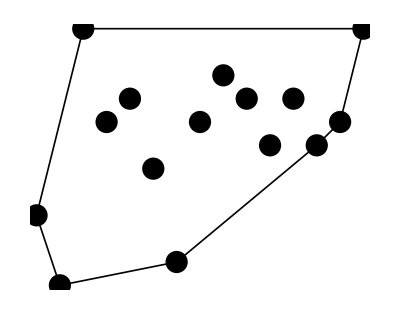

```mathematica
Show[Graphics[PlanarGraphPlot[lst,ConvexHull[lst],
DisplayFunction->Identity,LabelPoints->False][[1]]/. PointSize[x_]:>PointSize[.04]],AspectRatio->Automatic]
```